```mathematica
n=10;
x=Table[(i-1.)/n,{i,1,n+1}];
l = Table[1,{i,1,n+1}];
For[i=1,i≤n+1,i++,
For[k=1,k≤n+1,k++,
If[i≠k,
l[[i]]*= (y-x[[k]])/(x[[i]]-x[[k]]),];
];
];
```

```mathematica
points =Table[Sin[(i-1.)/n],{i,1,n+1}];
interpolant=0;
For[i=1,i≤n+1,i++,
interpolant += points[[i]]*l[[i]];
];
interpolant = Expand[interpolant]
```

0.+1. y-2.38288×10^-10 y^2-0.166667 y^3-1.90048×10^-8 y^4+0.00833341 y^5-2.04425×10^-7 y^6-0.000198053 y^7-4.18164×10^-7 y^8+3.06428×10^-6 y^9-1.31549×10^-7 y^10

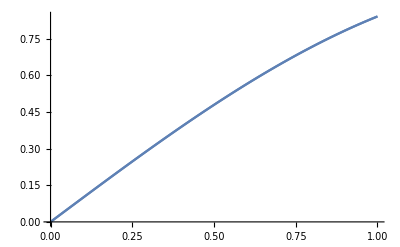

```mathematica
Show[Plot[Sin[y],{y,0,1}],Plot[interpolant, {y,0,1}]]
```

```mathematica
x
```

{0.,1.}

```mathematica
x
```

{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.}